```mathematica
(* occmax = 8 *)
```

{a→0.0000239786,b→6.44857}

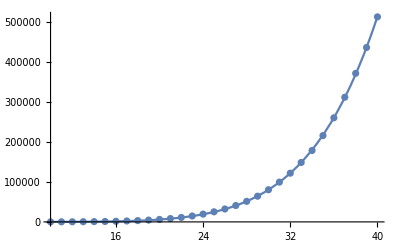

```mathematica
(* Basis size vs. Energy *)
x=Range[10,40];
y={116,186,293,460,706,1049,1590,2297,3261,4520,6170,8342,11157,14796,19471,25219,32287,40921,51419,64301,80421,99476,121851,148587,178643,215834,260320,311748,371498,436206,512821};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

{a→1.0934,b→2.92003}

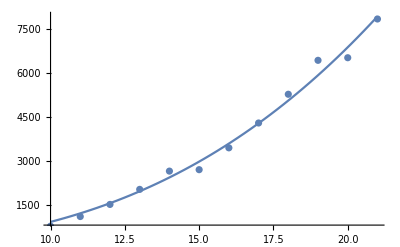

```mathematica
(* Number of operators vs. Energy *)
x={10,11,12,13,14,15,16,17,18,19,20,21};
y={764,1093,1507,2022,2647,2696,3443,4293,5276,6437,6526,7851};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

```mathematica
e=60;
(a*e^b*e/.{a->1.0933998100243698,b->2.920027336701123})
```

1.02136×10^7

{a→0.0000360917,b→7.79506}

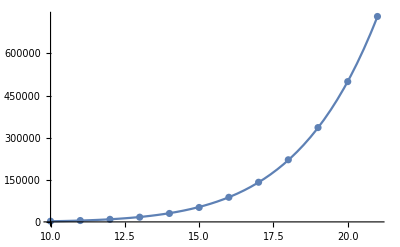

```mathematica
(* Nonzero matrix elements vs. Energy *)
x={10,11,12,13,14,15,16,17,18,19,20,21};
y={2533,4869,9128,16819,30043,51342,87567,141158,221180,335805,499469,731377};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

```mathematica
e=60;
(a*e^b/.{a->0.000036091748759696976,b->7.795057230401028})
(* size in bytes *)
(16*a*e^b/.{a->0.000036091748759696976,b->7.795057230401028})
```

2.61938×10^9

4.19101×10^10

```mathematica
(* Parametri relativi al generamento di VHH *)
```

```mathematica
data={
{21.0,29491,6340,1753,0.9190831184387207},{22.0,122411,7400,3775,1.7426042556762695},{23.0,271426,8488,6068,2.9301562309265137},{24.0,474799,9616,8633,4.746708869934082},{25.0,731934,10466,11412,6.7697930335998535},{26.0,1059434,12064,14600,9.651182413101196},{27.0,1455724,13651,18156,13.544855833053589},{28.0,1932711,15382,22171,18.993853092193604},{29.0,2472277,17055,26515,29.62894558906555},{30.0,3058154,18517,31006,39.4719500541687},{31.0,3734324,20925,35972,47.46139311790466},{32.0,4504708,23048,41398,51.51458787918091},{33.0,5393028,25525,47448,64.24801135063171},{34.0,6375648,27634,53964,77.88579487800598},{35.0,7414605,29395,60635,100.86894726753235},{36.0,8549129,32708,67689,117.99210000038147},{37.0,9819433,35818,75313,151.23246121406555},{38.0,11256934,39111,83752,199.6147072315216},{39.0,12839141,40340,92845,228.6237268447876},{40.0,14481524,44157,102048,252.38183283805847}
};
```

```mathematica
(* Number of non-zero matrix entries *)
nnz=data⟦All,{1,2}⟧
```

{{21.,29491},{22.,122411},{23.,271426},{24.,474799},{25.,731934},{26.,1059434},{27.,1455724},{28.,1932711},{29.,2472277},{30.,3058154},{31.,3734324},{32.,4504708},{33.,5393028},{34.,6375648},{35.,7414605},{36.,8549129},{37.,9819433},{38.,11256934},{39.,12839141},{40.,14481524}}

{a→5218.11,b→2.56639,c→-18.0668}

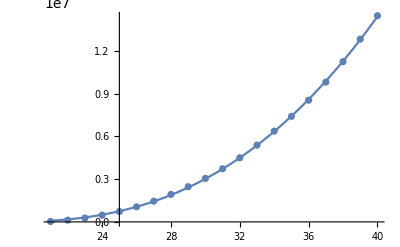

```mathematica
fit = FindFit[nnz, a*(z+c)^b,{a,b,c},z]
Show[Plot[a*(z+c)^b/.fit,{z,Min[nnz⟦All,1⟧],Max[nnz⟦All,1⟧]}],ListPlot[nnz]]
```

```mathematica
(* Estimate memory in bytes for sparse matrix *) 
a*(z+c)^b/.fit/.{z-> 60}
```

7.61424×10^7

```mathematica
(* size in MB *)
%*16/1000000
```

1218.28

```mathematica
(* Time spent to build the matrix *)
time=data⟦All,{1,5}⟧
zmin=20;
```

{{21.,0.919083},{22.,1.7426},{23.,2.93016},{24.,4.74671},{25.,6.76979},{26.,9.65118},{27.,13.5449},{28.,18.9939},{29.,29.6289},{30.,39.472},{31.,47.4614},{32.,51.5146},{33.,64.248},{34.,77.8858},{35.,100.869},{36.,117.992},{37.,151.232},{38.,199.615},{39.,228.624},{40.,252.382}}

{a→0.0244096,b→3.09296}

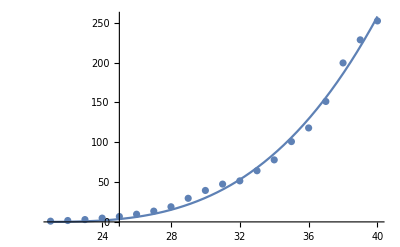

```mathematica
fit = FindFit[time, a*(z-zmin)^b,{a,b},z]
Show[Plot[a*(z-zmin)^b/.fit,{z,Min[time⟦All,1⟧],Max[time⟦All,1⟧]}],ListPlot[time]]
```

```mathematica
(* Estimated time spent to generate matrix *) 
a*(z-zmin)^b/.fit/.{z-> 60}
```

2201.27

```mathematica
(* in minutes *)
%/60
```

36.6878